# A DLA choir

## Jovana Andrejevic, Nina Andrejevic, Amina Matt, and George Varnavides

### We are combining audio with a DLA (Diffusion Limited Aggregation) algorithm.

### Sounds

#### Speak

```mathematica
Speak["Today we will program a DLA choir"]
```

#### A specific pitch with a duration and style

```mathematica
SoundNote[{"A1"},0.1,"VoiceAahs"]
```

SoundNote[{A1},0.1,VoiceAahs]

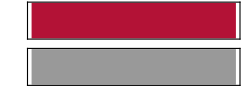

```mathematica
Sound[SoundNote[{"A1"},0.1,"VoiceAahs"]]
```

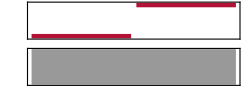

```mathematica
Sound[{SoundNote[{"C"},0.1,"VoiceAahs"],SoundNote[{"G"},0.1,"VoiceAahs"]}]
```

With the semitones given numerically and superposition

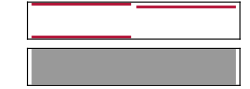

```mathematica
Sound[{SoundNote[{-5,7},0.1,"VoiceAahs"],SoundNote[6,0.1,"VoiceAahs"]}]
```

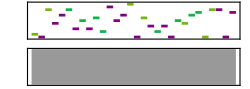

```mathematica
Sound[SoundNote[#,1,RandomChoice[{"Piano","Cello","Tuba"}]]& /@ RandomInteger[12, 30], 4]
```

#### An algorithmic composition with a Cellular Automaton

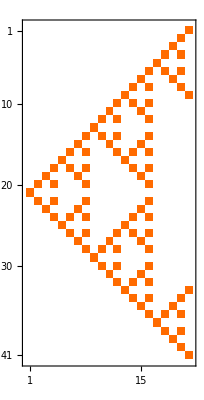

```mathematica
Transpose@CellularAutomaton[90,{{1},0},20]//MatrixPlot
```

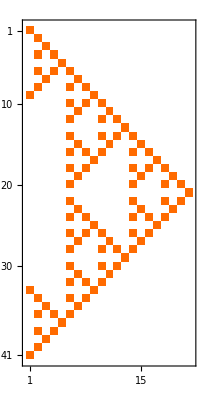

```mathematica
Reverse@#&/@Transpose[CellularAutomaton[90,{{1},0},20]]//MatrixPlot
```

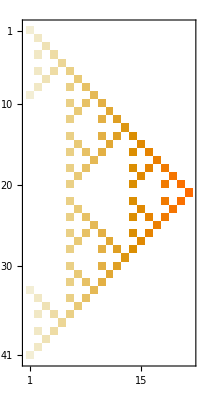

```mathematica
(3 Range[21]Reverse[#])&/@Transpose[CellularAutomaton[90,{{1},0},20]]//MatrixPlot
```

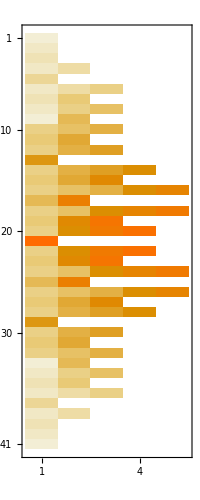

```mathematica
DeleteCases[(3 Range[21]Reverse[#]),0]&/@Transpose[CellularAutomaton[90,{{1},0},20]]//MatrixPlot
```

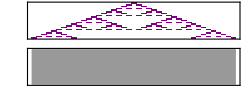

```mathematica
Sound[SoundNote[DeleteCases[3 Range[21]Reverse[#],0]-24(*3 octaves lower*),.1]&/@Transpose[CellularAutomaton[90,{{1},0},20]]]
```

#### From sinusoidal waves

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

Siren

```mathematica
f[t_,fc_,fm_,beta_]:=Sin[2*Pi*fc*t-beta*Sin[2*fm*Pi*t]]
```

```mathematica
f[t,1500,2,100]
```

Sin[3000 π t-100 Sin[4 π t]]

```mathematica
Sound[{Play[f[t,1500,2,100],{t,0,4}]}]
```

-Graphics-

```mathematica
Sound[{Play[f[t,1500,8,100],{t,0,4}]}]
```

-Graphics-

#### For our choir

```mathematica
lowNotes = {"A2","B2","C2", "D2", "E2","F2", "G2","A3","B3","C3", "D3", "E3","F3", "G3"};
```

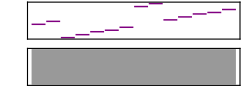

```mathematica
Sound[SoundNote[#]&/@lowNotes]
```

```mathematica
highNotes = {"A3","B3","C3", "D3", "E3","F3", "G3","A4","B4","C4", "D4", "E4","F4", "G4"};
```

```mathematica
Sound[SoundNote[#]&/@highNotes]
```

-Graphics-

```mathematica
notes:= Union[RandomSample[RandomChoice[{lowNotes,highNotes}], RandomInteger[{2,5}]]]
```

```mathematica
notes
```

{B3,E2,F3,G2}

```mathematica
sounds := {
(*{notes,0.2,"VoiceOohs"}*)
{notes,0.5,"VoiceAahs"}
}
```

```mathematica
sounds
```

{{{C3,E4},0.5,VoiceAahs}}

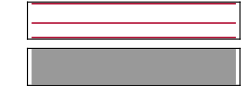

```mathematica
Sound[SoundNote@@RandomChoice[sounds]]
```

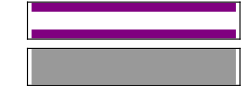

```mathematica
Sound[SoundNote[RandomChoice[sounds][[1]]]]
```

#### The DLA

#### A box with random walker starting along the edges

```mathematica
boxSize = 200;
alongEdge :=  RandomReal[{0,boxSize}];
numberWalkers = 75;
frozen = {{boxSize,boxSize}/2};
nf = Nearest[frozen];
```

```mathematica
(*A point somewhere on the fourth sides of the box*)
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}
]
```

```mathematica
walking = Table[launchPoint,{numberWalkers}];
```

```mathematica
walking
```

{{0,155.08},{55.1796,200},{200,14.0006},{0,79.3117},{191.962,0},{200,34.009},{200,133.398},{195.789,0},{34.0338,0},{126.583,0},{90.6913,0},{31.3159,200},{36.8107,0},{186.167,0},{0,41.4558},{126.596,200},{56.1731,0},{0.148848,200},{58.4766,0},{49.11,200},{193.223,200},{0,160.743},{135.138,200},{0,194.751},{177.529,0},{102.728,0},{43.5226,0},{9.6625,200},{140.369,200},{144.204,200},{183.229,0},{200,71.5711},{0,68.1173},{182.083,200},{200,160.447},{64.6453,200},{200,2.14233},{21.1012,0},{154.377,0},{0,120.038},{0,105.251},{37.8408,200},{165.856,200},{0,182.116},{72.5155,200},{200,22.4613},{0,6.21301},{179.723,200},{153.796,200},{200,59.3243},{200,71.6408},{158.615,200},{79.931,200},{200,117.288},{142.029,0},{113.828,200},{0,85.9513},{200,177.267},{157.137,200},{200,94.8874},{0,44.9733},{107.288,0},{0,59.8164},{117.166,0},{112.403,0},{16.3977,200},{22.0893,200},{0,91.8295},{61.0887,0},{169.892,200},{0,132.867},{169.397,0},{200,152.655},{0,1.30828},{21.9721,200}}

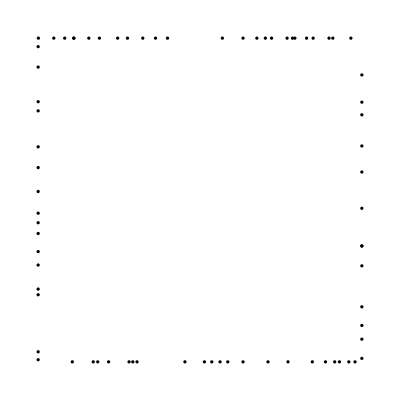

```mathematica
Graphics[{Disk[#]}&/@walking]
```

```mathematica
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]]
```

```mathematica
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize]
```

```mathematica
initialize:= Module[{},
boxSize = 200;
numberWalkers = 75;
frozen = {{boxSize,boxSize}/2};
walking = Table[launchPoint,{numberWalkers}];
nf = Nearest[frozen];
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}];
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]];
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize];
lowNotes = {"A2","B2","C2", "D2", "E2","F2", "G2","A3","B3","C3", "D3", "E3","F3", "G3"};
highNotes = {"A3","B3","C3", "D3", "E3","F3", "G3","A4","B4","C4", "D4", "E4","F4", "G4"};
notes:= Union[RandomSample[RandomChoice[{lowNotes,highNotes}], RandomInteger[{2,5}]]];
Sound[SoundNote[{"A"},0.1,"VoiceAahs"]];
sounds := {
(*{notes,0.2,"VoiceOohs"}*)
{notes,0.5,"VoiceAahs"}
};
]
```

```mathematica
dlaSimulaton:= 
Do[
walking = randomStep[#,2]&/@walking;
numberWalkers = Length[walking];
For[walker=1,walker≤ numberWalkers,walker++,
If[
squareDistanceToClosestFrozen[walking[[walker]],nf] ≤ 4,
(*Here is the sound*)
EmitSound@Sound[SoundNote@@RandomChoice[sounds]];
AppendTo[frozen,walking[[walker]]];
nf = Nearest[frozen];
walking[[walker]] = launchPoint;
];
]
,{100000}]
```

#### The EmitSound is necessary to Evaluate the wrapper.

#### With a nice interface

```mathematica
DefaultButton["Enjoy!",Speak["The push button is down at the bottom."];
CreateDocument[
{
Dynamic[
Graphics[
{
{FaceForm[RGBColor[0.65,0.74,1.]],EdgeForm[Black],Rectangle[{-1,-1},{boxSize+1,boxSize+1}]},
{GrayLevel[0.85],Disk[#,0.8]&/@walking},
{White,Disk[#,1.3]&/@frozen}
},
ImageSize-> Full
],Initialization:> initialize
],
DefaultButton["Push me!",dlaSimulaton,Method-> "Queued"]
}
],
Method->"Queued"
]
```

Enjoy!

```mathematica
frozen
```

{{100,100}}

#### With a signal when 5 of them have frozen and a techno touch

```mathematica
technoNotes = Table[i,{i,100,1000,100}];
```

```mathematica
f[t,#,2,100]&/@technoNotes
```

{Sin[200 π t-100 Sin[4 π t]],Sin[400 π t-100 Sin[4 π t]],Sin[600 π t-100 Sin[4 π t]],Sin[800 π t-100 Sin[4 π t]],Sin[1000 π t-100 Sin[4 π t]],Sin[1200 π t-100 Sin[4 π t]],Sin[1400 π t-100 Sin[4 π t]],Sin[1600 π t-100 Sin[4 π t]],Sin[1800 π t-100 Sin[4 π t]],Sin[2000 π t-100 Sin[4 π t]]}

```mathematica
(*EmitSound@*)Sound[{Play[f[t,#,2,100],{t,0,0.1}]}]&/@technoNotes
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
notes:= Union[RandomSample[RandomChoice[{technoNotes}], RandomInteger[{2,5}]]]
sounds := 
{Play[f[t,#,2,100],{t,0,0.2}]}&/@notes
```

```mathematica
sounds
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
initialize:= Module[{},
boxSize = 200;
numberWalkers = 150;
frozen = {{boxSize,boxSize}/2};
walking = Table[launchPoint,{numberWalkers}];
nf = Nearest[frozen];
launchPoint := 
RandomChoice[
{{0,alongEdge},{alongEdge,0},{boxSize, alongEdge},{alongEdge,boxSize}}];
squareDistanceToClosestFrozen[position_, nf_]:= SquaredEuclideanDistance[position,nf[position][[1]]];
randomStep[position_, dxMax_]:= Mod[position+ RandomReal[{0,dxMax}]Through[{Cos,Sin}[RandomReal[{0,2Pi}]]],boxSize];
(*Here*)
technoNotes = Table[i,{i,100,1000,100}];
notes:= Union[RandomSample[RandomChoice[{technoNotes}], RandomInteger[{2,5}]]];
sounds := 
{Play[f[t,#,2,100],{t,0,0.1}]}&/@notes;
;
]
```

#### Add the signal

```mathematica
siren=Sound[{Play[f[t,1500,2,100],{t,0,1}]}]
```

-Graphics-

```mathematica
If[
Mod[Dimensions[frozen][[1]],5]==0,EmitSound@siren,Nothing];
```

```mathematica
dlaSimulaton2:= 
Do[
walking = randomStep[#,2]&/@walking;
numberWalkers = Length[walking];
For[walker=1,walker≤ numberWalkers,walker++,
If[
squareDistanceToClosestFrozen[walking[[walker]],nf] ≤ 4,
(*Here is the signal*)
EmitSound@Sound[RandomChoice[sounds]];
If[Mod[Dimensions[frozen][[1]],5]==0,EmitSound@siren,Nothing];
AppendTo[frozen,walking[[walker]]];
nf = Nearest[frozen];
walking[[walker]] = launchPoint;
];
]
,{100000}]
```

```mathematica
DefaultButton["Enjoy!",Speak["The push button is down at the bottom."];
CreateDocument[
{
Dynamic[
Graphics[
{
{FaceForm[RGBColor[0.65,0.74,1.]],EdgeForm[Black],Rectangle[{-1,-1},{boxSize+1,boxSize+1}]},
{GrayLevel[0.85],Disk[#,0.8]&/@walking},
{White,Disk[#,1.3]&/@frozen}
},
ImageSize-> Full
],Initialization:> initialize
],
DefaultButton["Push me!",dlaSimulaton2,Method-> "Queued"]
}
],
Method->"Queued"
]
```

Enjoy!